# Recompiling to SingleQubitAndCNOT

```mathematica
SetDirectory @ NotebookDirectory[];
Import["../Link/QuESTlink.m"];
```

```mathematica
testRecomp[gate_, showGates:(True|False):True] := Module[
	{recomp, error},
	recomp = RecompileCircuit[gate, "SingleQubitAndCNOT"];
	error = CalcCircuitMatrix[gate] - CalcCircuitMatrix[N@recomp] // Abs // Max;
	error = error // FullSimplify // Chop;
	If[showGates, Echo @ recomp];
	Echo @ DrawCircuit[{{gate}, recomp}];
	Echo[error, "error: "];
	If[error =!= 0, Style["ERRONEOUS DECOMPOSITION!", Red]]]
```

```mathematica
?QuEST`Gate`*
```

## Testing doc

```mathematica
?RecompileCircuit
```

## Testing decomp gates

### G

```mathematica
testRecomp @ G[x]
```

{G[x]}

-Graphics-

error:   0

### H

```mathematica
testRecomp @ Subscript[H, 0]
```

{H_0}

-Graphics-

error:   0

### Id

```mathematica
testRecomp @ Subscript[Id, 0,1]
```

{Id_(0,1)}

-Graphics-

error:   0

### Ph

```mathematica
testRecomp @ Subscript[Ph, 0][θ]
```

{Ph_0[θ]}

-Graphics-

error:   0

### Rx, Ry, Rz

```mathematica
testRecomp @ Subscript[Rx, 0][θ]
```

{Rx_0[θ]}

-Graphics-

error:   0

```mathematica
testRecomp @ Subscript[Ry, 0][θ]
```

{Ry_0[θ]}

-Graphics-

error:   0

```mathematica
testRecomp @ Subscript[Rz, 0][θ]
```

{Rz_0[θ]}

-Graphics-

error:   0

### S

```mathematica
testRecomp @ Subscript[S, 0]
```

{S_0}

-Graphics-

error:   0

### T

```mathematica
testRecomp @ Subscript[T, 0]
```

{T_0}

-Graphics-

error:   0

### X, Y, Z

```mathematica
testRecomp @ Subscript[X, 0]
```

{X_0}

-Graphics-

error:   0

```mathematica
testRecomp @ Subscript[Y, 0]
```

{Y_0}

-Graphics-

error:   0

```mathematica
testRecomp @ Subscript[Z, 0]
```

{Z_0}

-Graphics-

error:   0

## Testing canonical gates

## Un-controlled

### Ph

{Ph_1[x/2],Ph_0[x/2],C_0[X_1],Ph_1[-x/2],C_0[X_1]}

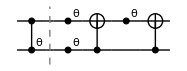

error:   0

```mathematica
testRecomp @ Subscript[Ph, 0,1][x]
```

{Ph_1[x/4],Ph_2[x/4],C_2[X_1],Ph_1[-x/4],C_2[X_1],Ph_0[x/4],Ph_2[x/4],C_2[X_0],Ph_0[-x/4],C_2[X_0],H_1,C_0[X_1],Ph_1[-π/4],C_2[X_1],T_1,C_0[X_1],Ph_1[-π/4],C_2[X_1],T_1,T_0,C_2[X_0],T_2,Ph_0[-π/4],C_2[X_0],H_1,Ph_1[-x/4],Ph_2[-x/4],C_2[X_1],Ph_1[x/4],C_2[X_1],H_1,C_0[X_1],Ph_1[-π/4],C_2[X_1],T_1,C_0[X_1],Ph_1[-π/4],C_2[X_1],T_1,T_0,C_2[X_0],T_2,Ph_0[-π/4],C_2[X_0],H_1}

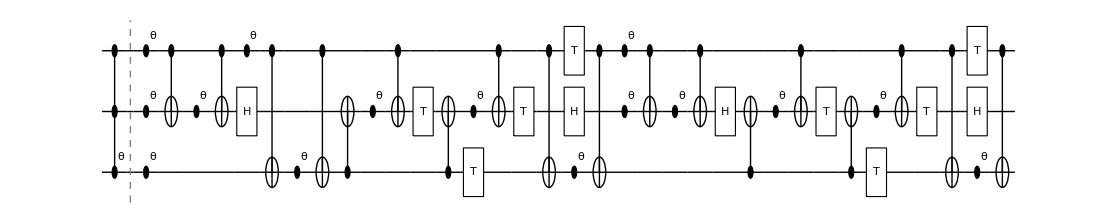

error:   0

```mathematica
testRecomp @ Subscript[Ph, 0,1,2][x]
```

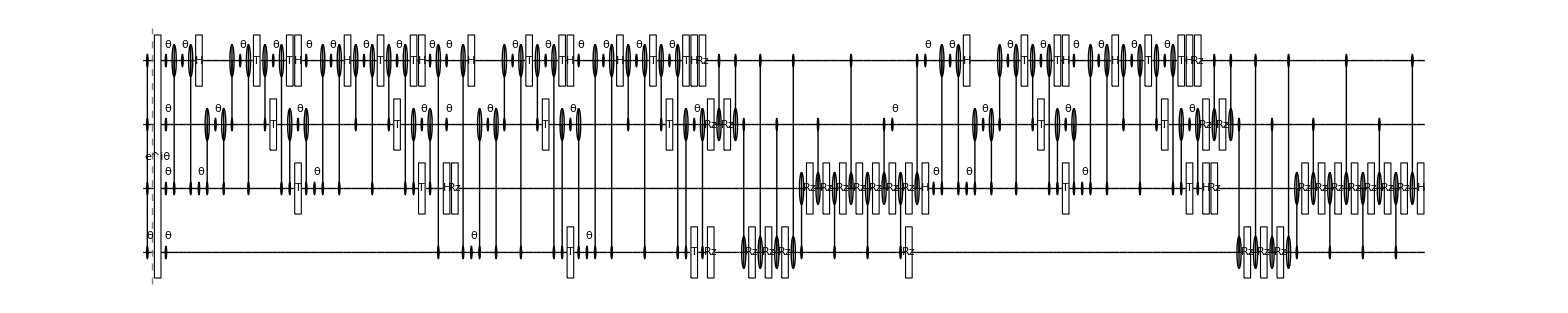

error:   0

```mathematica
testRecomp[Subscript[Ph, 0,1,2,3][-1.2], False]
```

### R

```mathematica
testRecomp @ R[x, Subscript[X, 0]]
testRecomp @ R[x, Subscript[Y, 0]]
testRecomp @ R[x, Subscript[Z, 0]]
```

{Rx_0[x]}

-Graphics-

error:   0

{Ry_0[x]}

-Graphics-

error:   0

{Rz_0[x]}

-Graphics-

error:   0

{H_0,C_0[X_1],Ry_1[x],C_0[X_1],H_0}

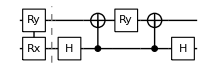

error:   0

```mathematica
testRecomp @ R[x, Subscript[X, 0] Subscript[Y, 1]]
```

{C_0[X_1],Ry_1[x],C_0[X_1]}

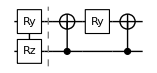

error:   0

```mathematica
testRecomp @ R[x, Subscript[Z, 0] Subscript[Y, 1]]
```

{H_1,C_1[X_0],Rz_0[x],C_1[X_0],H_1}

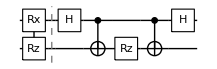

error:   0

```mathematica
testRecomp @ R[x, Subscript[Z, 0] Subscript[X, 1]]
```

{C_3[X_2],H_0,C_0[X_2],H_1,C_1[X_2],H_4,C_4[X_2],Ry_2[x],C_4[X_2],H_4,C_1[X_2],H_1,C_0[X_2],H_0,C_3[X_2]}

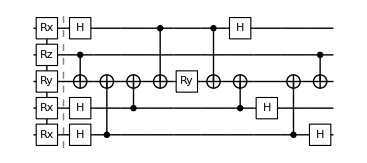

error:   0

```mathematica
testRecomp @ R[x, Subscript[X, 0] Subscript[X, 1] Subscript[Y, 2] Subscript[Z, 3] Subscript[X, 4]]
```

### Rz^(n)

{C_1[X_0],C_2[X_0],Rz_0[x],C_2[X_0],C_1[X_0]}

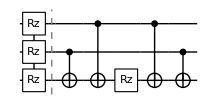

error:   0

```mathematica
testRecomp @ Subscript[Rz, 0,1,2][x]
```

### SWAP

{C_0[X_1],C_1[X_0],C_0[X_1]}

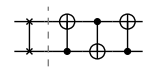

error:   0

```mathematica
testRecomp @ Subscript[SWAP, 0,1]
```

## Singly-controlled

### C[G]

```mathematica
(* cannot draw ill-formed input *)
```

```mathematica
DrawCircuit @ RecompileCircuit[Subscript[C, 0]@G[x], "SingleQubitAndCNOT"]
```

DrawCircuit::error: Invalid arguments. See ?DrawCircuit

$Failed

### C[H]

{Ph_1[-π/2],H_1,Ph_1[-π/4],C_0[X_1],T_1,H_1,S_1}

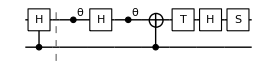

error:   0

```mathematica
testRecomp @ Subscript[C, 0][Subscript[H, 1]]
```

### C[Ph]

```mathematica
testRecomp @ Subscript[C, 0][Subscript[Ph, 1][x]]
```

{Ph_1[x/2],Ph_0[x/2],C_0[X_1],Ph_1[-x/2],C_0[X_1]}

-Graphics-

error:   0

### C[R]

{Rz_0[π/2],Ry_0[x/2],C_1[X_0],Ry_0[-x/2],C_1[X_0],Rz_0[-π/2]}

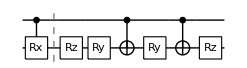

error:   0

{Ry_0[x/2],C_1[X_0],Ry_0[-x/2],C_1[X_0]}

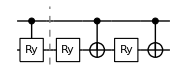

error:   0

{Rz_0[x/2],C_1[X_0],Rz_0[-x/2],C_1[X_0]}

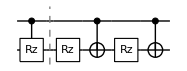

error:   0

```mathematica
testRecomp @ Subscript[C, 1]@ R[x, Subscript[X, 0]]
testRecomp @ Subscript[C, 1]@ R[x, Subscript[Y, 0]]
testRecomp @ Subscript[C, 1]@ R[x, Subscript[Z, 0]]
```

{H_0,C_0[X_1],H_4,C_4[X_1],Ry_1[x/2],C_2[X_1],Ry_1[-x/2],C_2[X_1],C_4[X_1],H_4,C_0[X_1],H_0}

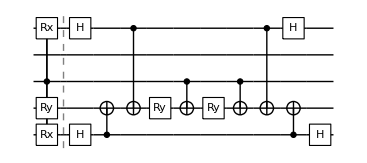

error:   0

```mathematica
testRecomp @ Subscript[C, 2]@R[x, Subscript[X, 0] Subscript[Y, 1] Subscript[X, 4]]
```

### C[Rx]

```mathematica
testRecomp @ Subscript[C, 1]@Subscript[Rx, 0][x]
```

{Rz_0[π/2],Ry_0[x/2],C_1[X_0],Ry_0[-x/2],C_1[X_0],Rz_0[-π/2]}

-Graphics-

error:   0

### C[Ry], C[Rz]

```mathematica
testRecomp @ Subscript[C, 1]@Subscript[Ry, 0][x]
```

{Ry_0[x/2],C_1[X_0],Ry_0[-x/2],C_1[X_0]}

-Graphics-

error:   0

```mathematica
testRecomp @ Subscript[C, 1]@Subscript[Rz, 0][x]
```

{Rz_0[x/2],C_1[X_0],Rz_0[-x/2],C_1[X_0]}

-Graphics-

error:   0

### C[S], C[T]

{Ph_0[π/4],Ph_1[π/4],C_1[X_0],Ph_0[-π/4],C_1[X_0]}

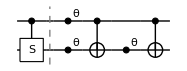

error:   0

```mathematica
testRecomp @ Subscript[C, 1]@Subscript[S, 0]
```

{Ph_0[π/8],Ph_1[π/8],C_1[X_0],Ph_0[-π/8],C_1[X_0]}

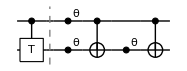

error:   0

```mathematica
testRecomp @ Subscript[C, 1]@Subscript[T, 0]
```

### C[SWAP]

{C_0[X_2],H_0,C_1[X_2],T_0,Ph_2[-π/4],T_1,C_0[X_2],C_1[X_0],T_2,C_1[X_2],Ph_0[-π/4],Ph_2[-π/4],C_1[X_0],C_0[X_2],H_0,T_2,C_0[X_2]}

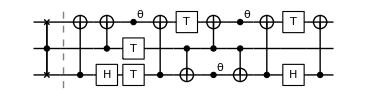

error:   0

```mathematica
testRecomp @ Subscript[C, 1]@Subscript[SWAP, 0,2]
```

### C[Y]

{Ph_0[-π/2],C_1[X_0],S_0}

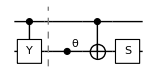

error:   0

```mathematica
testRecomp @ Subscript[C, 1]@Subscript[Y, 0]
```

### C[Z]

{H_0,C_1[X_0],H_0}

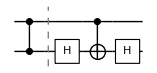

error:   0

```mathematica
testRecomp @ Subscript[C, 1]@Subscript[Z, 0]
```

## Multi-controlled

### C*[G]

```mathematica
(* cannot draw ill-formed input *)
```

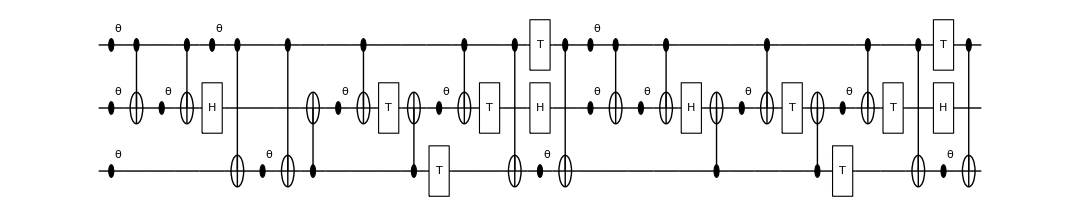

```mathematica
DrawCircuit @ RecompileCircuit[Subscript[C, 0,1,2]@G[x], "SingleQubitAndCNOT"]
```

### C*[H]

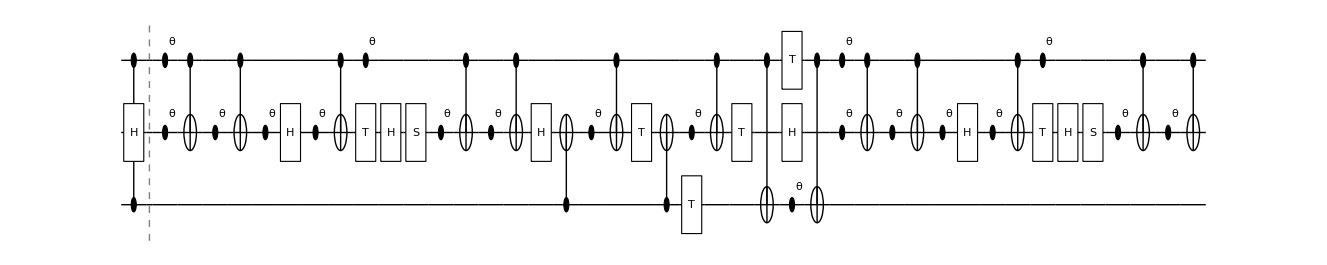

error:   0

```mathematica
testRecomp[Subscript[C, 0,2][Subscript[H, 1]], False]
```

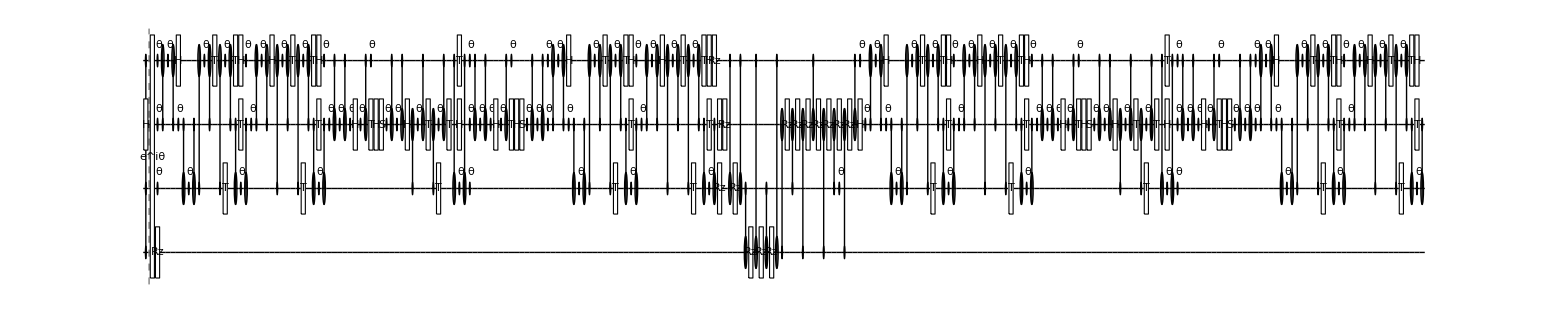

error:   0

```mathematica
testRecomp[Subscript[C, 0,1,3][Subscript[H, 2]], False]
```

### C*[Ph]

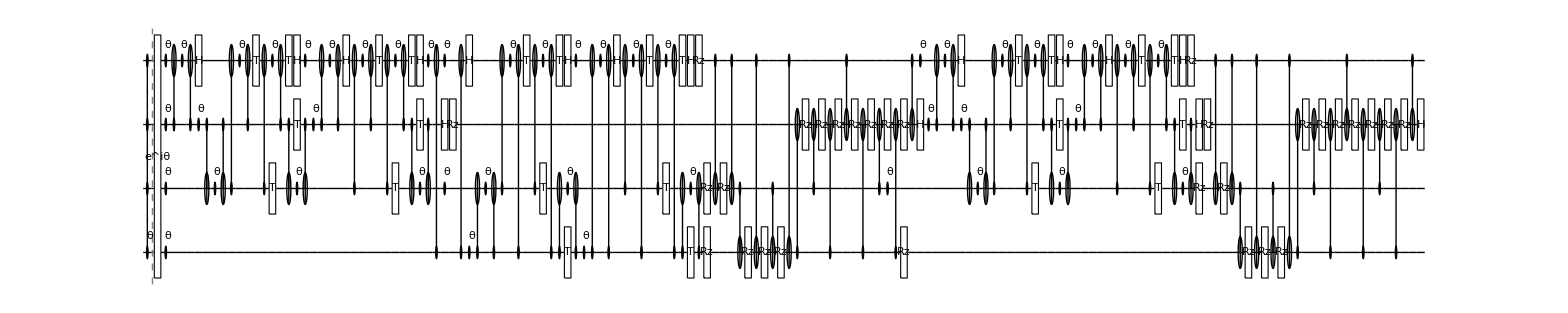

error:   0

```mathematica
testRecomp[Subscript[C, 0,2][Subscript[Ph, 1,3][.1]], False]
```

### C*[R]

{Rz_0[π/2],Ry_0[-0.025],C_1[X_0],Ry_0[0.025],C_1[X_0],Rz_0[-π/2],C_2[X_1],Rz_0[π/2],Ry_0[0.025],C_1[X_0],Ry_0[-0.025],C_1[X_0],Rz_0[-π/2],C_2[X_1],Rz_0[π/2],Ry_0[-0.025],C_2[X_0],Ry_0[0.025],C_2[X_0],Rz_0[-π/2]}

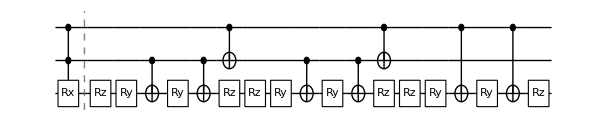

error:   0

{Ry_0[x/4],C_1[X_0],Ry_0[-x/4],C_1[X_0],C_2[X_1],Ry_0[-x/4],C_1[X_0],Ry_0[x/4],C_1[X_0],C_2[X_1],Ry_0[x/4],C_2[X_0],Ry_0[-x/4],C_2[X_0]}

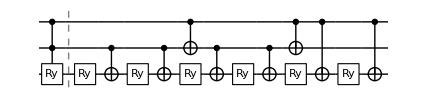

error:   0

{Rz_0[x/4],C_1[X_0],Rz_0[-x/4],C_1[X_0],C_2[X_1],Rz_0[-x/4],C_1[X_0],Rz_0[x/4],C_1[X_0],C_2[X_1],Rz_0[x/4],C_2[X_0],Rz_0[-x/4],C_2[X_0]}

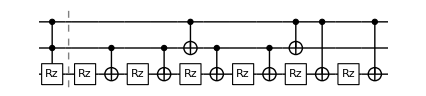

error:   0

```mathematica
testRecomp @ Subscript[C, 1,2]@ R[-.1, Subscript[X, 0]]
testRecomp @ Subscript[C, 1,2]@ R[x, Subscript[Y, 0]]
testRecomp @ Subscript[C, 1,2]@ R[x, Subscript[Z, 0]]
```

{H_0,C_0[X_1],H_4,C_4[X_1],Ry_1[x/4],C_2[X_1],Ry_1[-x/4],C_2[X_1],C_3[X_2],Ry_1[-x/4],C_2[X_1],Ry_1[x/4],C_2[X_1],C_3[X_2],Ry_1[x/4],C_3[X_1],Ry_1[-x/4],C_3[X_1],C_4[X_1],H_4,C_0[X_1],H_0}

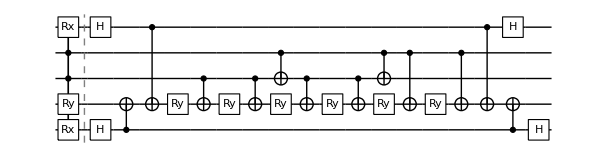

error:   0

```mathematica
testRecomp @ Subscript[C, 2,3]@R[x, Subscript[X, 0] Subscript[Y, 1] Subscript[X, 4]]
```

### C*[Rx]

{Rz_3[π/2],Ry_3[0.025],C_0[X_3],Ry_3[-0.025],C_0[X_3],Rz_3[-π/2],C_1[X_0],Rz_3[π/2],Ry_3[-0.025],C_0[X_3],Ry_3[0.025],C_0[X_3],Rz_3[-π/2],C_1[X_0],Rz_3[π/2],Ry_3[0.025],C_1[X_3],Ry_3[-0.025],C_1[X_3],Rz_3[-π/2]}

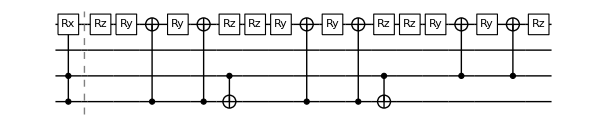

error:   0

```mathematica
testRecomp @ Subscript[C, 0,1][Subscript[Rx, 3][.1]]
```

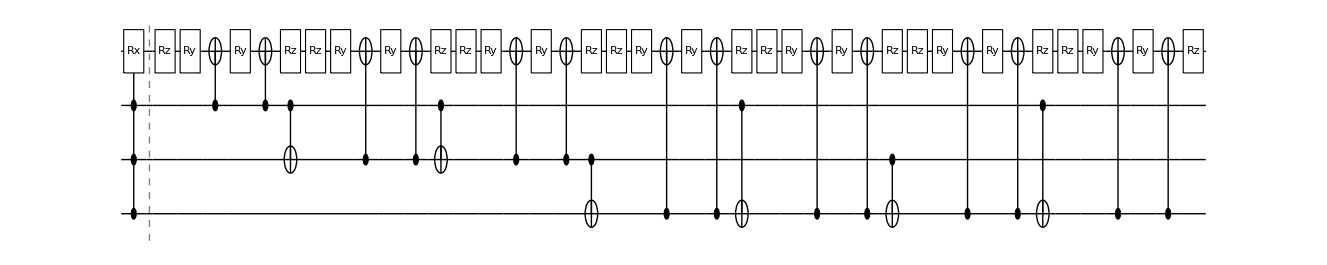

error:   0

```mathematica
testRecomp[ Subscript[C, 0,1,2][Subscript[Rx, 3][.1]], False]
```

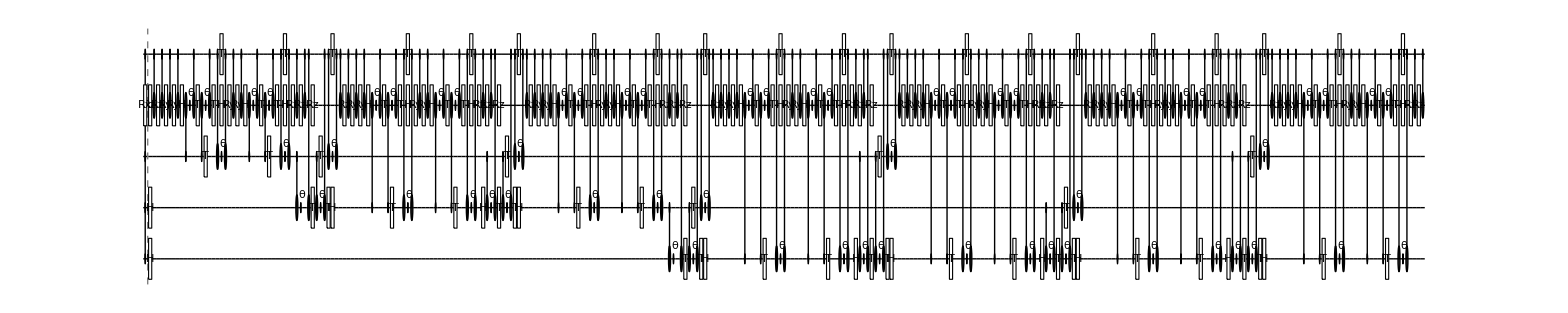

error:   0

```mathematica
testRecomp[Subscript[C, 0,1,2,4][Subscript[Rx, 3][.1]], False]
```

### C*[Ry]

{Ry_3[x/4],C_0[X_3],Ry_3[-x/4],C_0[X_3],C_1[X_0],Ry_3[-x/4],C_0[X_3],Ry_3[x/4],C_0[X_3],C_1[X_0],Ry_3[x/4],C_1[X_3],Ry_3[-x/4],C_1[X_3]}

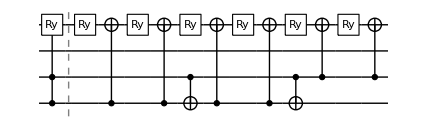

error:   0

```mathematica
testRecomp @ Subscript[C, 0,1][Subscript[Ry, 3][x]]
```

{Ry_3[0.0125],C_2[X_3],Ry_3[-0.0125],C_2[X_3],C_2[X_1],Ry_3[-0.0125],C_1[X_3],Ry_3[0.0125],C_1[X_3],C_2[X_1],Ry_3[0.0125],C_1[X_3],Ry_3[-0.0125],C_1[X_3],C_1[X_0],Ry_3[-0.0125],C_0[X_3],Ry_3[0.0125],C_0[X_3],C_2[X_0],Ry_3[0.0125],C_0[X_3],Ry_3[-0.0125],C_0[X_3],C_1[X_0],Ry_3[-0.0125],C_0[X_3],Ry_3[0.0125],C_0[X_3],C_2[X_0],Ry_3[0.0125],C_0[X_3],Ry_3[-0.0125],C_0[X_3]}

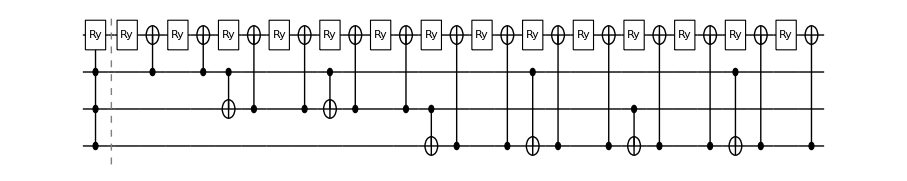

error:   0

```mathematica
testRecomp @ Subscript[C, 0,1,2][Subscript[Ry, 3][.1]]
```

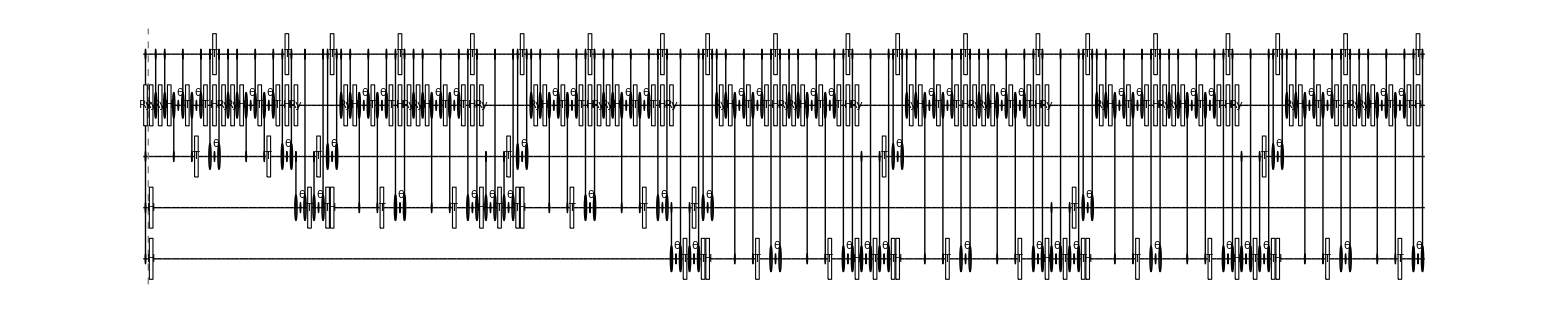

error:   0

```mathematica
testRecomp[Subscript[C, 0,1,2,4][Subscript[Ry, 3][.1]], False]
```

### C*[Rz]

{Rz_3[x/4],C_0[X_3],Rz_3[-x/4],C_0[X_3],C_1[X_0],Rz_3[-x/4],C_0[X_3],Rz_3[x/4],C_0[X_3],C_1[X_0],Rz_3[x/4],C_1[X_3],Rz_3[-x/4],C_1[X_3]}

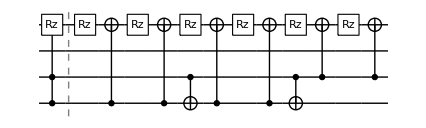

error:   0

```mathematica
testRecomp @ Subscript[C, 0,1][Subscript[Rz, 3][x]]
```

{Rz_3[0.0125],C_2[X_3],Rz_3[-0.0125],C_2[X_3],C_2[X_1],Rz_3[-0.0125],C_1[X_3],Rz_3[0.0125],C_1[X_3],C_2[X_1],Rz_3[0.0125],C_1[X_3],Rz_3[-0.0125],C_1[X_3],C_1[X_0],Rz_3[-0.0125],C_0[X_3],Rz_3[0.0125],C_0[X_3],C_2[X_0],Rz_3[0.0125],C_0[X_3],Rz_3[-0.0125],C_0[X_3],C_1[X_0],Rz_3[-0.0125],C_0[X_3],Rz_3[0.0125],C_0[X_3],C_2[X_0],Rz_3[0.0125],C_0[X_3],Rz_3[-0.0125],C_0[X_3]}

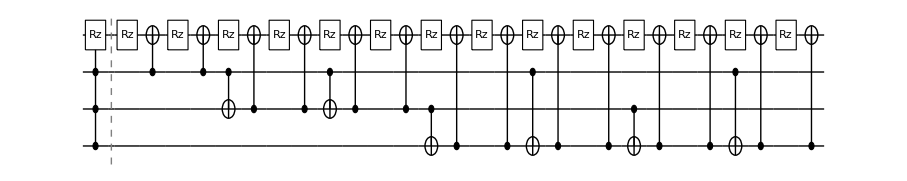

error:   0

```mathematica
testRecomp @ Subscript[C, 0,1,2][Subscript[Rz, 3][.1]]
```

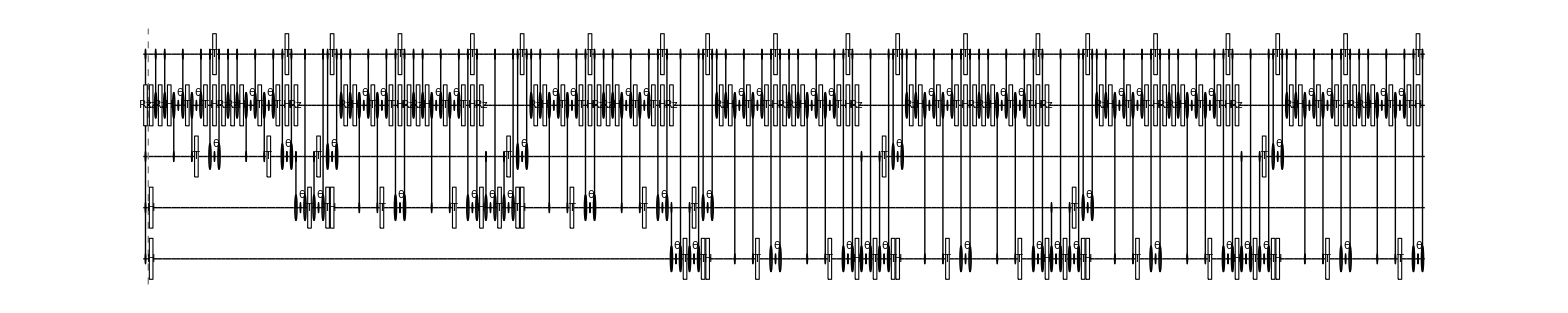

error:   0

```mathematica
testRecomp[Subscript[C, 0,1,2,4][Subscript[Rz, 3][.1]], False]
```

### C*[S]

{Ph_1[π/8],Ph_2[π/8],C_2[X_1],Ph_1[-π/8],C_2[X_1],Ph_0[π/8],Ph_2[π/8],C_2[X_0],Ph_0[-π/8],C_2[X_0],H_1,C_0[X_1],Ph_1[-π/4],C_2[X_1],T_1,C_0[X_1],Ph_1[-π/4],C_2[X_1],T_1,T_0,C_2[X_0],T_2,Ph_0[-π/4],C_2[X_0],H_1,Ph_1[-π/8],Ph_2[-π/8],C_2[X_1],Ph_1[π/8],C_2[X_1],H_1,C_0[X_1],Ph_1[-π/4],C_2[X_1],T_1,C_0[X_1],Ph_1[-π/4],C_2[X_1],T_1,T_0,C_2[X_0],T_2,Ph_0[-π/4],C_2[X_0],H_1}

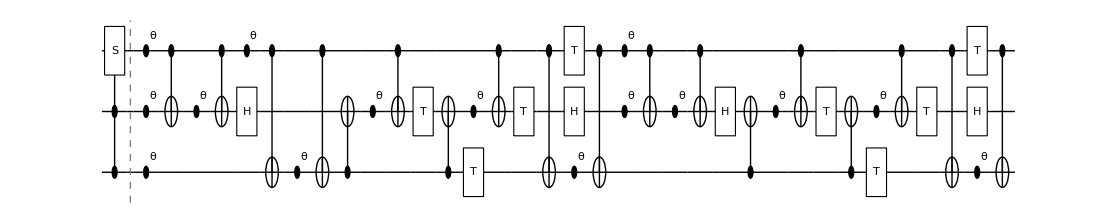

error:   0

```mathematica
testRecomp @ Subscript[C, 0,1][Subscript[S, 2]]
```

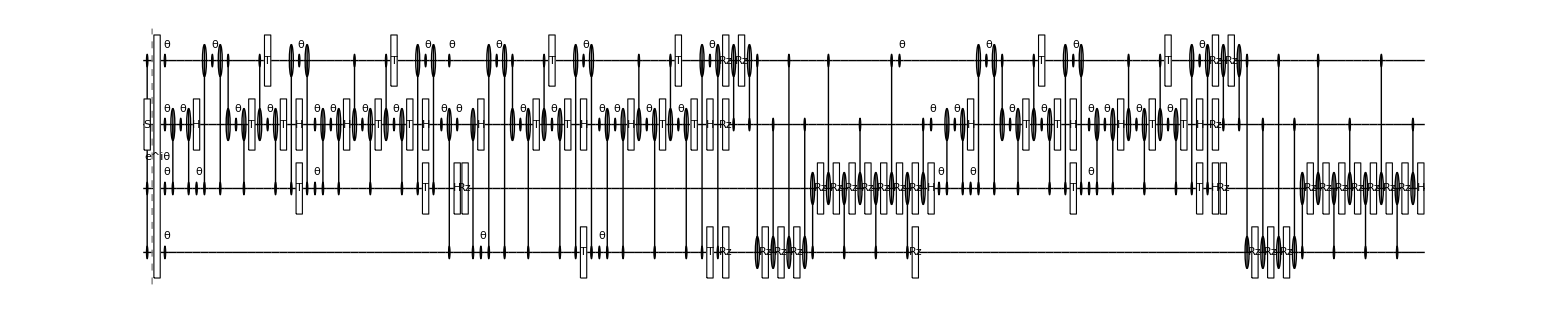

error:   0

```mathematica
testRecomp[Subscript[C, 0,1,3][Subscript[S, 2]], False]
```

### C*[T]

{Ph_1[π/16],Ph_2[π/16],C_2[X_1],Ph_1[-π/16],C_2[X_1],Ph_0[π/16],Ph_2[π/16],C_2[X_0],Ph_0[-π/16],C_2[X_0],H_1,C_0[X_1],Ph_1[-π/4],C_2[X_1],T_1,C_0[X_1],Ph_1[-π/4],C_2[X_1],T_1,T_0,C_2[X_0],T_2,Ph_0[-π/4],C_2[X_0],H_1,Ph_1[-π/16],Ph_2[-π/16],C_2[X_1],Ph_1[π/16],C_2[X_1],H_1,C_0[X_1],Ph_1[-π/4],C_2[X_1],T_1,C_0[X_1],Ph_1[-π/4],C_2[X_1],T_1,T_0,C_2[X_0],T_2,Ph_0[-π/4],C_2[X_0],H_1}

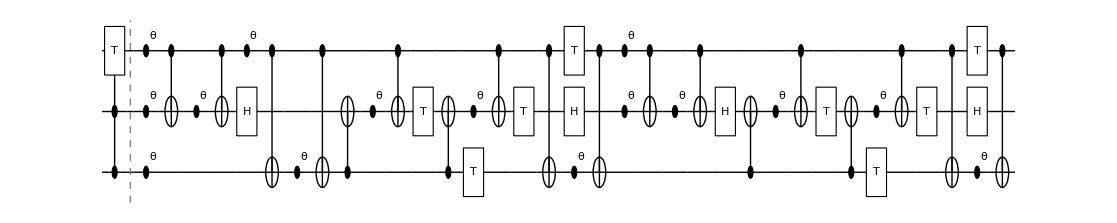

error:   0

```mathematica
testRecomp @ Subscript[C, 0,1][Subscript[T, 2]]
```

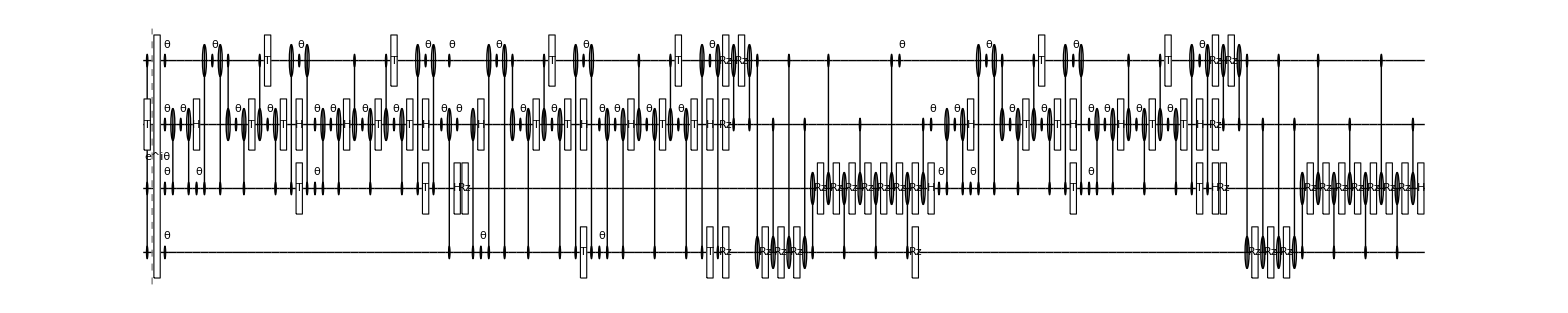

error:   0

```mathematica
testRecomp[Subscript[C, 0,1,3][Subscript[T, 2]], False]
```

### C*[X]

{H_2,C_0[X_2],Ph_2[-π/4],C_1[X_2],T_2,C_0[X_2],Ph_2[-π/4],C_1[X_2],T_2,T_0,C_1[X_0],T_1,Ph_0[-π/4],C_1[X_0],H_2}

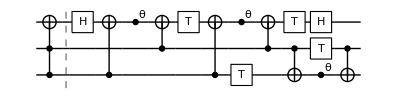

error:   0

```mathematica
testRecomp @ Subscript[C, 0,1][Subscript[X, 2]]
```

{G[π/16],H_2,Rz_0[π/8],Rz_1[π/8],Rz_3[π/8],Rz_2[π/8],C_3[X_1],Rz_1[-π/8],C_3[X_1],C_1[X_0],Rz_0[-π/8],C_3[X_0],Rz_0[π/8],C_1[X_0],Rz_0[-π/8],C_3[X_0],C_0[X_2],Rz_2[-π/8],C_1[X_2],Rz_2[π/8],C_0[X_2],Rz_2[-π/8],C_3[X_2],Rz_2[π/8],C_0[X_2],Rz_2[-π/8],C_1[X_2],Rz_2[π/8],C_0[X_2],Rz_2[-π/8],C_3[X_2],H_2}

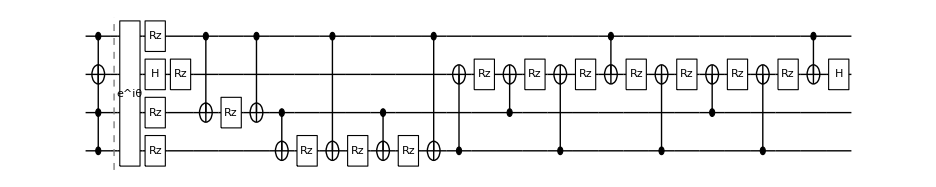

error:   0

```mathematica
testRecomp @ Subscript[C, 0,1,3][Subscript[X, 2]]
```

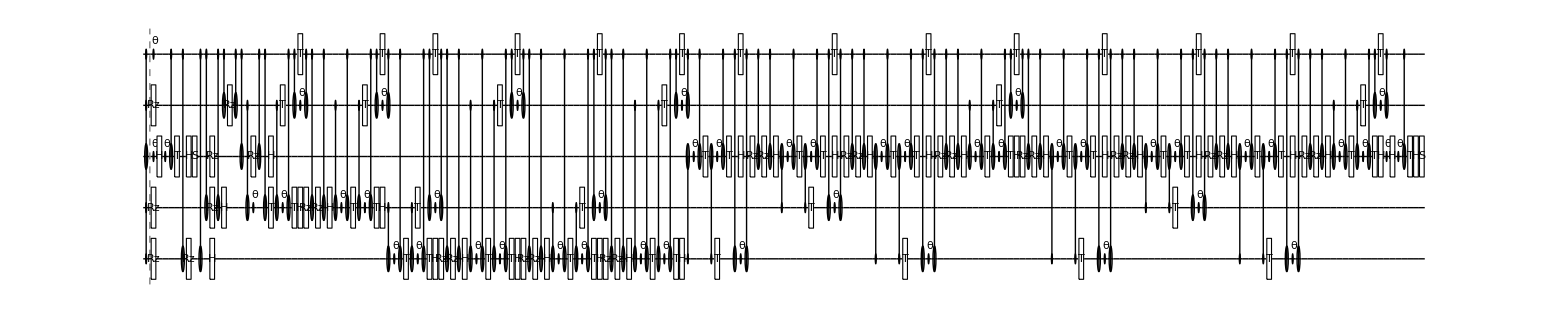

error:   0

```mathematica
testRecomp[Subscript[C, 0,1,3,4][Subscript[X, 2]], False]
```

### C*[Y]

{Ph_2[-π/4],Ph_1[-π/4],C_1[X_2],Ph_2[π/4],C_1[X_2],H_2,C_0[X_2],Ph_2[-π/4],C_1[X_2],T_2,C_0[X_2],Ph_2[-π/4],C_1[X_2],T_2,T_0,C_1[X_0],T_1,Ph_0[-π/4],C_1[X_0],H_2,Ph_2[π/4],Ph_1[π/4],C_1[X_2],Ph_2[-π/4],C_1[X_2]}

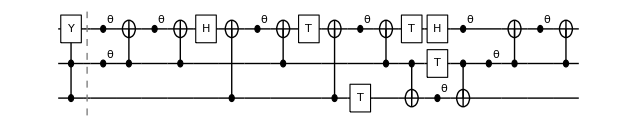

error:   0

```mathematica
testRecomp @ Subscript[C, 0,1][Subscript[Y, 2]]
```

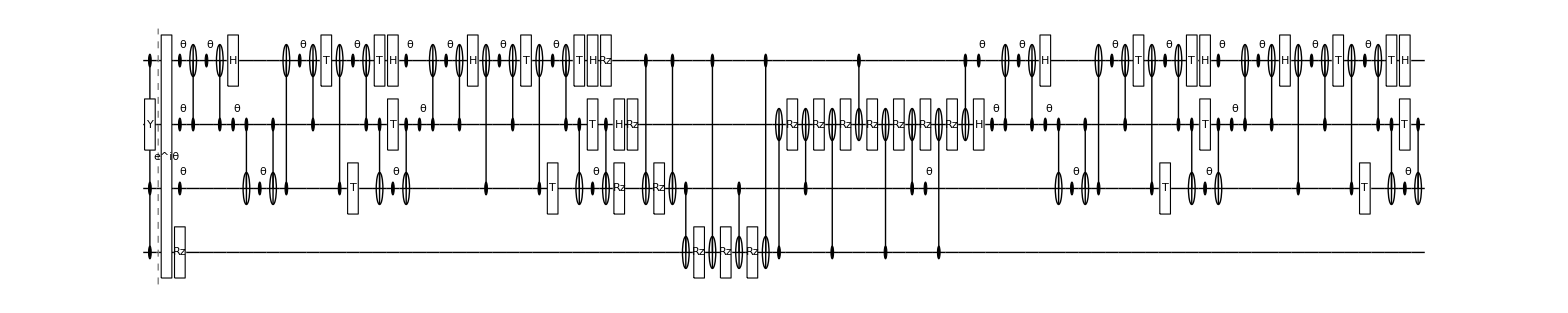

error:   0

```mathematica
testRecomp[ Subscript[C, 0,1,3][Subscript[Y, 2]], False]
```

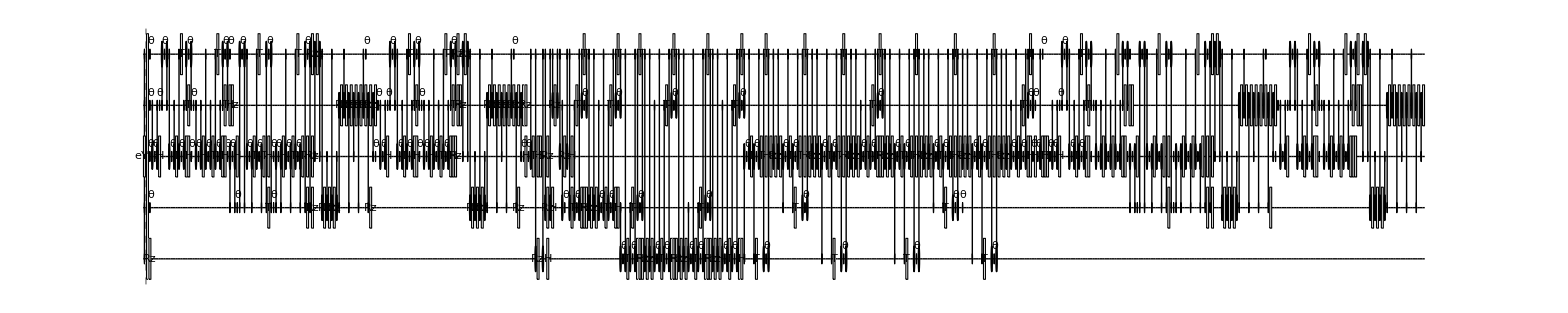

error:   0

```mathematica
testRecomp[ Subscript[C, 0,1,3,4][Subscript[Y, 2]], False]
```

### C*[Z]

{C_0[X_2],Ph_2[-π/4],C_1[X_2],T_2,C_0[X_2],Ph_2[-π/4],C_1[X_2],T_2,T_0,C_1[X_0],T_1,Ph_0[-π/4],C_1[X_0]}

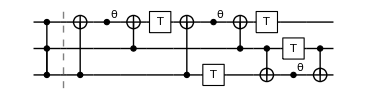

error:   0

```mathematica
testRecomp @ Subscript[C, 0,1][Subscript[Z, 2]]
```

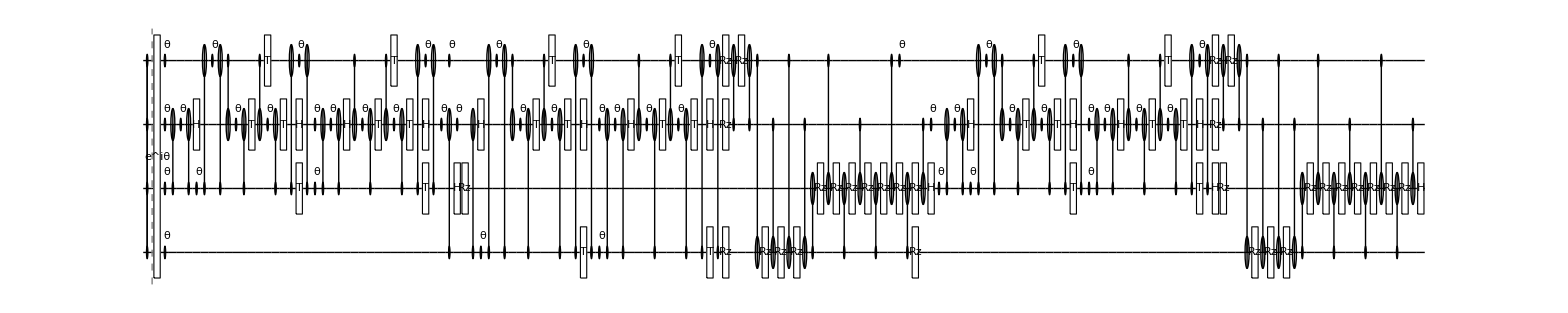

error:   0

```mathematica
testRecomp[ Subscript[C, 0,1,3][Subscript[Z, 2]], False]
```

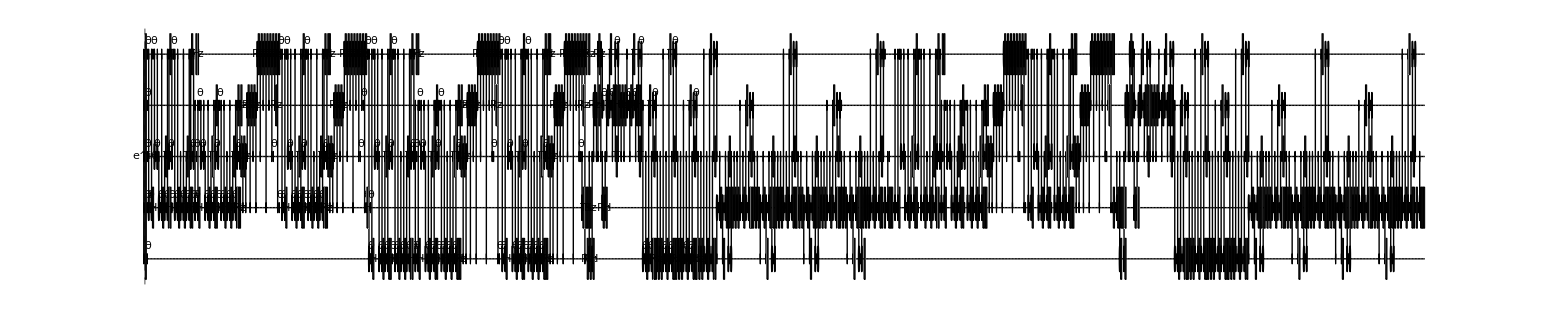

error:   0

```mathematica
testRecomp[ Subscript[C, 0,1,3,4][Subscript[Z, 2]], False]
```

### C*[SWAP]

{G[π/16],C_2[X_3],H_2,Rz_0[π/8],Rz_1[π/8],Rz_3[π/8],Rz_2[π/8],C_3[X_1],Rz_1[-π/8],C_3[X_1],C_1[X_0],Rz_0[-π/8],C_3[X_0],Rz_0[π/8],C_1[X_0],Rz_0[-π/8],C_3[X_0],C_0[X_2],Rz_2[-π/8],C_1[X_2],Rz_2[π/8],C_0[X_2],Rz_2[-π/8],C_3[X_2],Rz_2[π/8],C_0[X_2],Rz_2[-π/8],C_1[X_2],Rz_2[π/8],C_0[X_2],Rz_2[-π/8],C_3[X_2],H_2,C_2[X_3]}

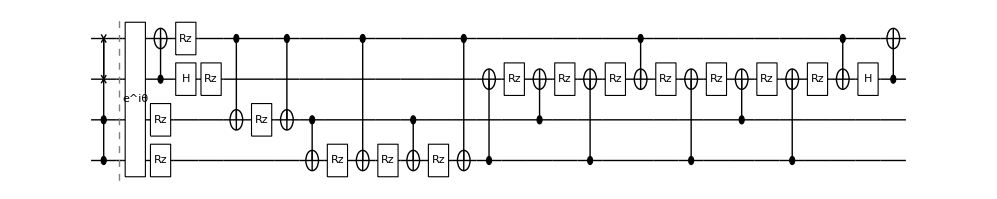

error:   0

```mathematica
testRecomp @ Subscript[C, 0,1][Subscript[SWAP, 2,3]]
```

## Testing U (matrix)

## Un-controlled

### U^(1)

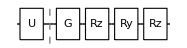

error:   0

```mathematica
testRecomp[Subscript[U, 0] @ RandomVariate @ CircularUnitaryMatrixDistribution @ 2, False]
```

```mathematica
testRecomp[Subscript[U, 0] @ {{Exp[ⅈ .1],0},{0,Exp[-ⅈ π/3]}}, False]
```

-Graphics-

error:   0

```mathematica
RecompileCircuit[ Subscript[U, 0]@{{a,b},{c,d}}, "SingleQubitAndCNOT"]
```

{G[ArcTan[Re[a],Im[a]]+1/2 (-2 ArcTan[Re[a],Im[a]]+ArcTan[-Re[b],-Im[b]]+ArcTan[Re[c],Im[c]])],Rz_0[-ArcTan[Re[a],Im[a]]+ArcTan[-Re[b],-Im[b]]],Ry_0[2 ArcTan[Abs[b]/Abs[a]]],Rz_0[-ArcTan[Re[a],Im[a]]+ArcTan[Re[c],Im[c]]]}

### U^(n)

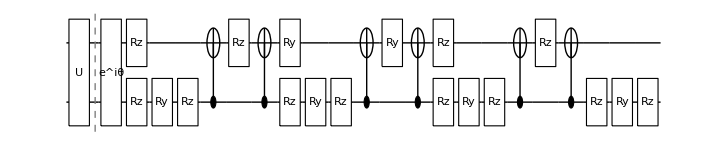

error:   0

```mathematica
testRecomp[Subscript[U, 0,1] @ RandomVariate @ CircularUnitaryMatrixDistribution[2^2], False]
```

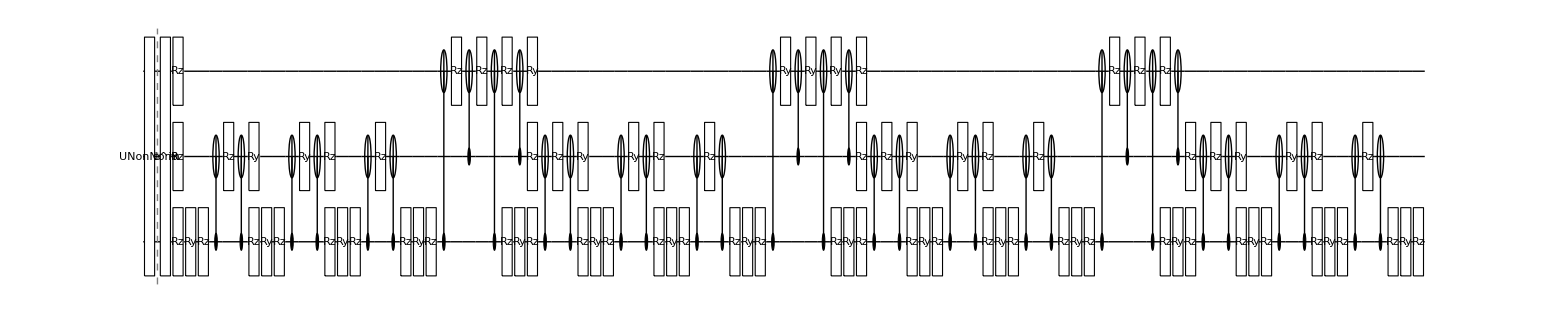

error:   0

```mathematica
testRecomp[Subscript[UNonNorm, 0,1,2] @ RandomVariate @ CircularUnitaryMatrixDistribution[2^3], False]
```

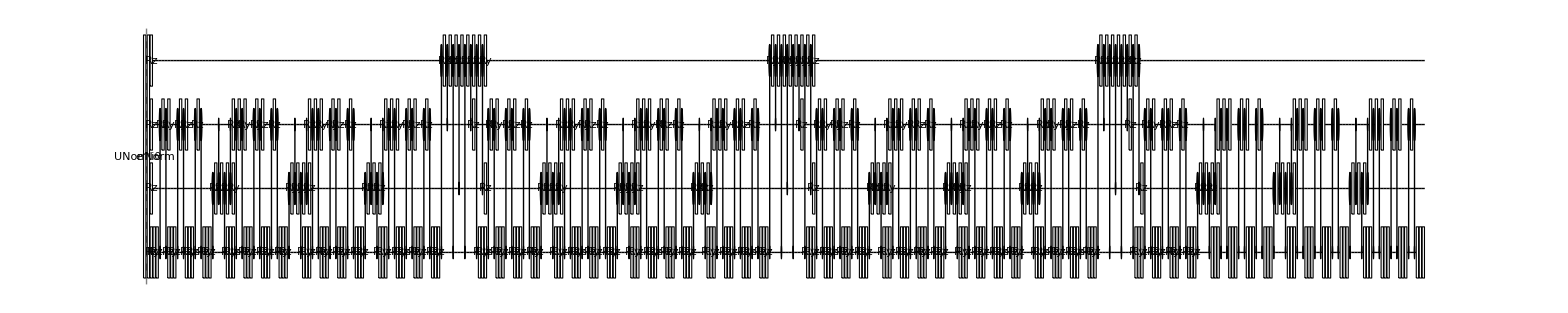

error:   0

```mathematica
testRecomp[Subscript[UNonNorm, 0,2,1,3] @ RandomVariate @ CircularUnitaryMatrixDistribution[2^4], False]
```

## Singly-controlled

### C[U^(1)]

{Rz_1[-1.56961],C_0[X_1],Rz_1[-1.62996],Ry_1[-0.645443],C_0[X_1],Ry_1[0.645443],Rz_1[3.19956],Ph_0[-0.693822]}

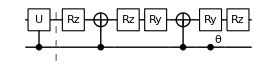

error:   0

```mathematica
testRecomp[Subscript[C, 0]@Subscript[U, 1] @ RandomVariate @ CircularUnitaryMatrixDistribution @ 2]
```

{Rz_0[0.573599],C_1[X_0],Rz_0[0.573599],C_1[X_0],Rz_0[-1.1472],Ph_1[-0.473599]}

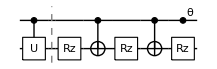

error:   0

```mathematica
testRecomp[Subscript[C, 1]@Subscript[U, 0] @ {{Exp[ⅈ .1],0},{0,Exp[-ⅈ π/3]}}]
```

### C[U^(n )]

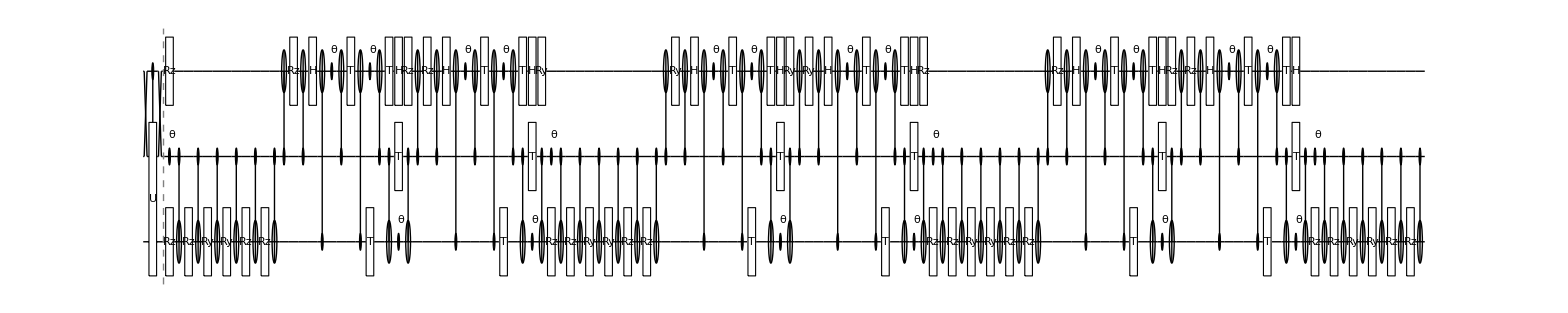

error:   0

```mathematica
testRecomp[Subscript[C, 1]@Subscript[U, 0,2] @ RandomVariate @ CircularUnitaryMatrixDistribution[2^2], False]
```

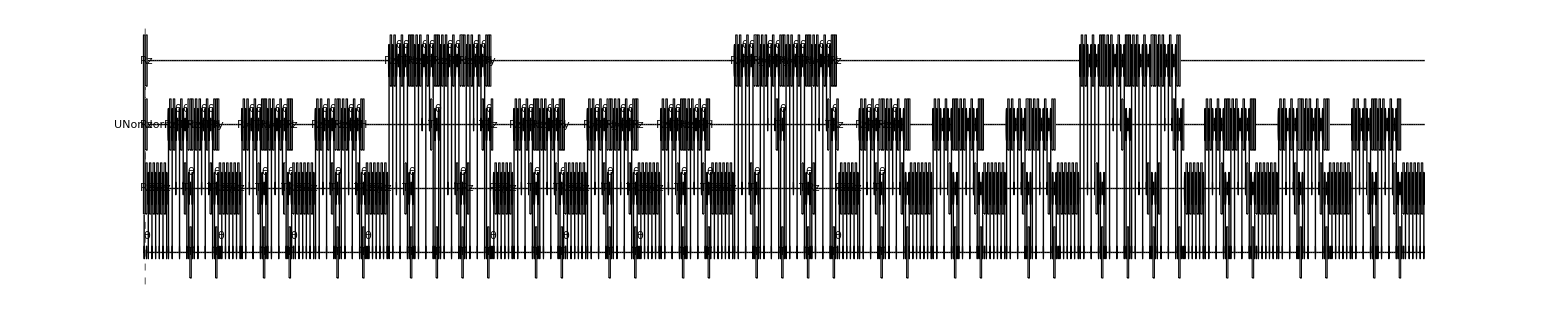

error:   0

```mathematica
testRecomp[Subscript[C, 0]@Subscript[UNonNorm, 1,2,3] @ RandomVariate @ CircularUnitaryMatrixDistribution[2^3], False]
```

## Multi-controlled

### C*[U^(1)]

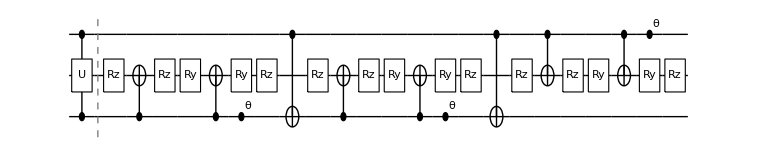

error:   0

```mathematica
testRecomp[Subscript[C, 0,2]@Subscript[U, 1] @ RandomVariate @ CircularUnitaryMatrixDistribution @ 2, False]
```

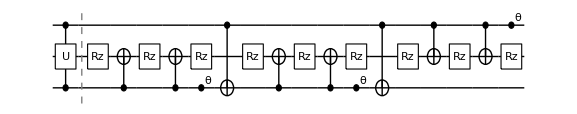

error:   0

```mathematica
testRecomp[Subscript[C, 0,2]@Subscript[U, 1] @ {{Exp[ⅈ .1],0},{0,Exp[-ⅈ π/3]}}, False]
```

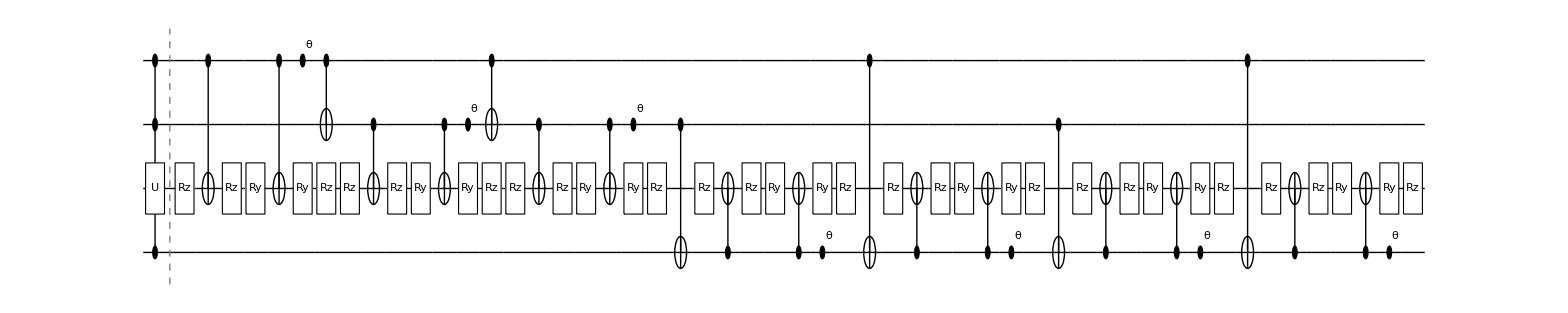

error:   0

```mathematica
testRecomp[Subscript[C, 0,2,3]@Subscript[U, 1] @ RandomVariate @ CircularUnitaryMatrixDistribution @ 2, False]
```

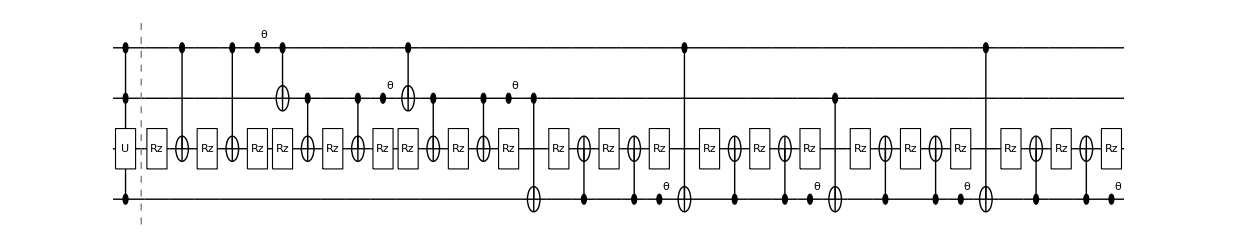

error:   0

```mathematica
testRecomp[Subscript[C, 0,2,3]@Subscript[U, 1] @ {{Exp[ⅈ .1],0},{0,Exp[-ⅈ π/3]}}, False]
```

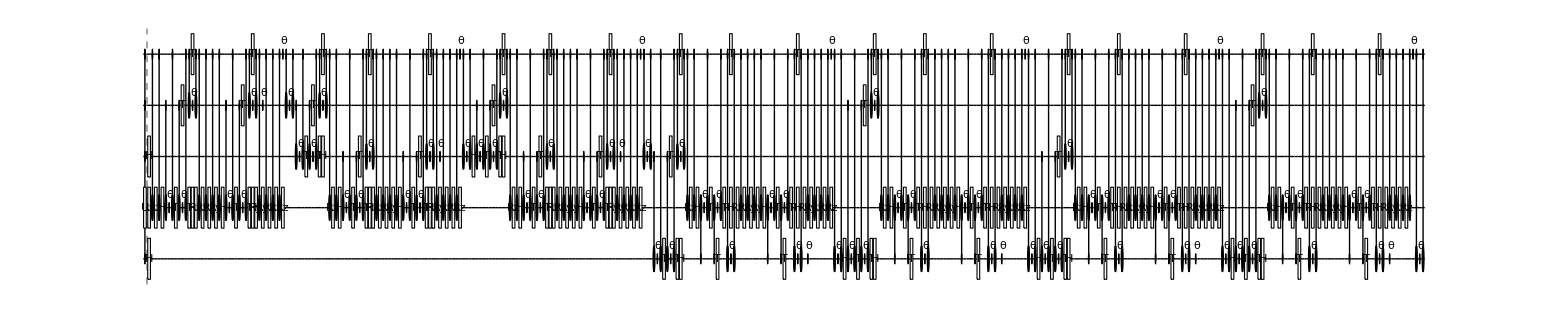

error:   0

```mathematica
testRecomp[Subscript[C, 0,2,3,4]@Subscript[U, 1] @ RandomVariate @ CircularUnitaryMatrixDistribution @ 2, False]
```

### C*[U^(n )]

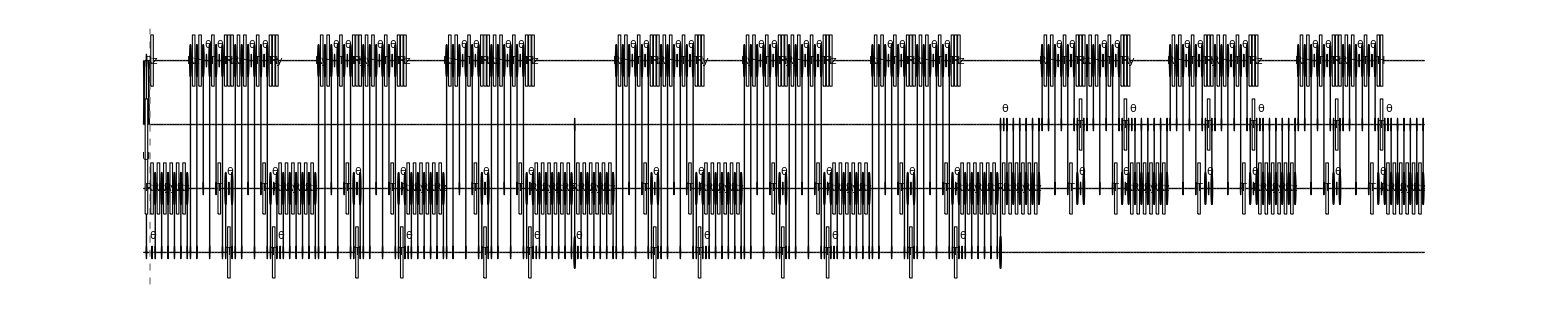

error:   0

```mathematica
testRecomp[Subscript[C, 0,2]@Subscript[U, 1,3] @ RandomVariate @ CircularUnitaryMatrixDistribution[2^2], False]
```

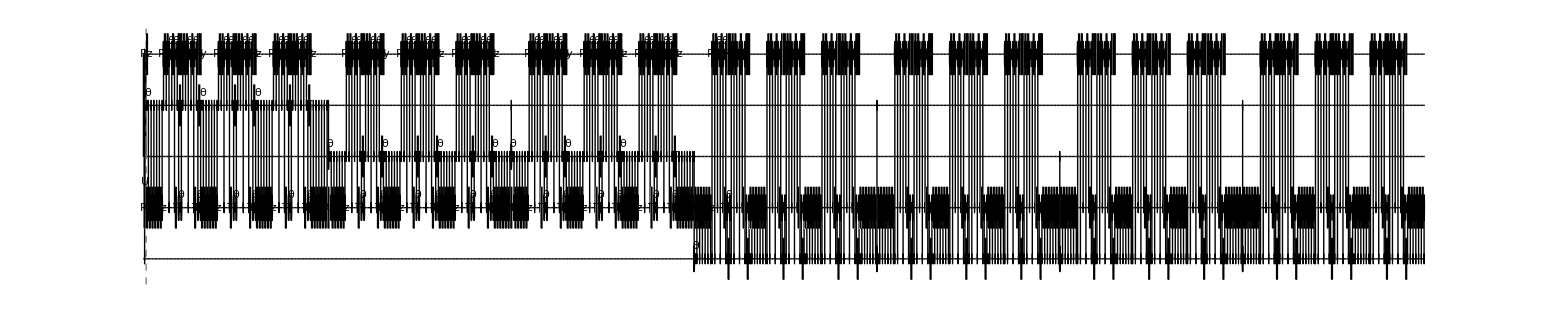

error:   0

```mathematica
testRecomp[Subscript[C, 0,2,3]@Subscript[U, 1,4] @ RandomVariate @ CircularUnitaryMatrixDistribution[2^2], False]
```

## Testing U (vector)

## Un-controlled

### U^(1)

```mathematica
testRecomp @ Subscript[U, 0][{Exp[ⅈ .2],Exp[ - ⅈ π/3]}]
```

{G[-0.423599],Rz_0[-1.2472]}

-Graphics-

error:   0

### U^(n )

not yet supported

## Singly-controlled

### C[U^(1)]

not yet supported

### C[U^(n )]

not yet supported

## Multi-controlled

### C*[U^(1)]

not yet supported

### C*[U^(n )]

not yet supported

## Testing errors

### invalid arguments

```mathematica
RecompileCircuit[bleh]
```

RecompileCircuit::error: Invalid arguments. See ?RecompileCircuit

$Failed

### unrecognised method

```mathematica
RecompileCircuit[Subscript[X, 0], "eh"]
```

RecompileCircuit::error: Unrecognised method. See available methods via ?RecompileCircuit

### unrecognised gates

```mathematica
RecompileCircuit[{Subscript[Y, 0],Subscript[Poop, 0],Subscript[X, 0], Subscript[Blob, 3]}, "SingleQubitAndCNOT"]
```

RecompileCircuit::error: Recompilation failed. Could not recompile unrecognised gate: Poop_0

$Failed

### unsupported gates

```mathematica
RecompileCircuit[Subscript[Damp, 0][x], "SingleQubitAndCNOT"]
```

RecompileCircuit::error: Recompilation failed. Could not recompile unrecognised gate: Damp_0[x]

$Failed

```mathematica
RecompileCircuit[Subscript[U, 0,1] @ {a,b,c,d}, "SingleQubitAndCNOT"]
```

RecompileCircuit::error: Recompilation failed. Many-qubit diagonal gates are not yet supported by the recompiler.

$Failed

```mathematica
RecompileCircuit[Subscript[C, 1,2]@Subscript[U, 0] @ {a,b}, "SingleQubitAndCNOT"]
```

RecompileCircuit::error: Recompilation failed. Controlled diagonal gates are not yet supported by the recompiler.

$Failed

### numerical issues

```mathematica
RecompileCircuit[
	Subscript[U, 0,1][{{a,b},{c,d}}],
	"SingleQubitAndCNOT"]
```

RecompileCircuit::error: Recompilation failed. Encountered a non-numerical matrix in a two (or more) qubit U gate, which cannot be decomposed.

$Failed

```mathematica
RecompileCircuit[
	Subscript[U, 0,1] @ RandomComplex[{-ⅈ-1,ⅈ+1}, {2^2,2^2}],
	"SingleQubitAndCNOT"]
```

RecompileCircuit::error: Recompilation failed. Encountered a non-unitary U gate matrix which cannot be (spectrally) decomposed. Please use UNonNorm instead.

$Failed

```mathematica
RecompileCircuit[
	Subscript[U, 0,1] @  (2 IdentityMatrix @ 4),
	"SingleQubitAndCNOT"]
```

RecompileCircuit::error: Recompilation failed. The cosine-sine decomposition involved in recompiling a U (or UNonNorm) gate failed.

$Failed